Copyright (C) 2010 Jonathan Manton (jmanton @ illinois.edu)

This program is free software; you can redistribute it and/or modify it under the terms of the GNU General Public License as published by the Free Software Foundation; either version 2 of the License, or (at your option) any later version.

This program is distributed in the hope that it will be useful, but WITHOUT ANY WARRANTY; without even the implied warranty of MERCHANTABILITY or FITNESS FOR A PARTICULAR PURPOSE.  See the# GNU General Public License for more details.

You should have received a copy of the GNU General Public License along with this program; if not, write to the Free Software Foundation, Inc., 59 Temple Place, Suite 330, Boston, MA  02111-1307  USA

```mathematica
plotTab[theta_, minOffset_, tabAngle_, minTablength_, tabHeight_] := (
If[minOffset > tabHeight, mo = tabHeight, mo = minOffset];
topLimitLine = {Dashed, Line[{{0,0}, {100 Cos[theta], 100 Sin[theta]}}]}; 
bottomLine = {Line[{{0,0},{100,0}}]};
tabLine = {Dotted, Line[{{0,tabHeight}, {100,tabHeight}}]};

bX = mo Cot[theta];
aX = bX - (mo Cot[tabAngle]);
b = {Point[{bX,0}],Line[{{bX,0},{bX,mo}}]};
a = {Point[{aX,0}],Line[{{aX,0},{bX,mo}}]};
bmult = 100/(Cos[theta] Sin[tabAngle]/Sin[theta] +Cos[tabAngle]);
tiY = bmult Sin[tabAngle];
tiX = 100-(bmult Cos[tabAngle]);

checkline = {{Line[{{tiX,0},{tiX, tiY}}],Red,Line[{{0,tiY},{100,tiY}}],Line[{{100,0},{100 - 100 Cos[tabAngle],100 Sin[tabAngle]}}]}};
If[theta ≥ tabAngle,
tabLeft = {{0,0}, {tabHeight/Sin[tabAngle] Cos[tabAngle],tabHeight}},
tabLeft = {{0,0}, {aX, 0}, {bX, mo}}
];
If[tiY > tabHeight, tiY = tabHeight];
tabRight = {{100-tiY/Sin[tabAngle]Cos[tabAngle],tiY},{100,0}};
tab = {{Blue, Line[Join[tabLeft,tabRight]]}};
Graphics[{tab,b,topLimitLine, bottomLine,tabLine}]
)
```

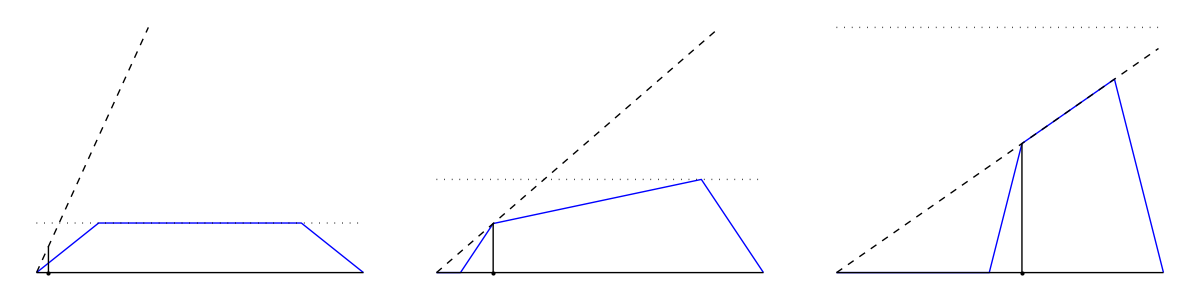

```mathematica
tabAngle = 45; height = 19;
minheight = 10;
Grid[{{plotTab[70 Degree, minheight, tabAngle Degree, 40, height],plotTab[30 Degree, minheight, tabAngle Degree, 40, height],plotTab[10 Degree, minheight, tabAngle Degree, 40, height]}}]
```